```mathematica
resultX = LaplaceTransform[HeavisideTheta[t],t,s];
```

```mathematica
resultW = 10/(1+(1+0.46s));
```

```mathematica
function = InverseLaplaceTransform[resultW*resultX,s,t];
```

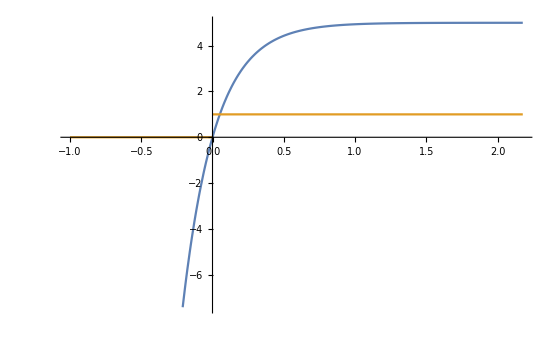

```mathematica
Plot[{function,HeavisideTheta[t]},{t,-1.0,2.177199}]
```

```mathematica
impuls = InverseLaplaceTransform[resultW/resultX,s,t];
```

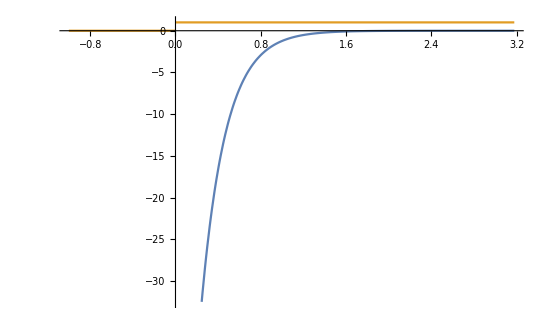

```mathematica
Plot[{impuls,HeavisideTheta[t]},{t,-1.0,3.177199}]
```